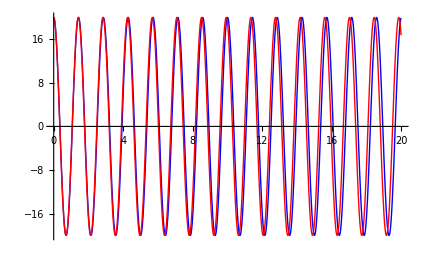
```mathematica
g=9.8;
 
(*grav. constant*)
l=0.5; (*length of pendulum*)

θ0=20*π/180; (*20 degrees*)
ω0 = 0; (*starting from rest*)
(*ϕ=y;
t=x;*)
ode1={θ''[t]==-(g/l)*Sin[θ[t]],θ[0]==θ0,θ'[0]==ω0};
sol=NDSolve[ode1,θ,{t,0,20}];
myplot1 = Plot[(180/Pi) θ[t]/.sol,{t,0,20},PlotStyle-> RGBColor[0,0,1],PlotRange-> All];
omega=√(g/l);
approx = (180/Pi) θ0 Cos[omega*t];
myplot2=Plot[approx,{t,0,20},PlotStyle-> RGBColor[1,0,0],PlotRange-> All];

Show[{myplot1,myplot2}]
-Graphics-
Manipulate[
g=9.8; l=0.5; omega=√(g/l);
Module[
{result = NDSolve[{θ''[t]==-(g/l)*Sin[θ[t]],θ[0]==θ0,θ'[0]==ω0},θ, {t, 0,20}]},
Plot[{(180/Pi) θ0 Cos[omega*t],(180/Pi)* θ[t]/.result},{t,0,20},PlotStyle-> {{Blue},{Dashed,Red}},PlotRange-> All,AxesLabel->{"t (s)","θ (rad)"},PlotRange->{{0,20},{-20,20}},ImageSize->{500,300}]],
{{l,0.5,"length (m)"},0,2,Appearance->"Labeled"},{{θ0,20*Pi/180,"initial angle (rad)"},.1,π/2,Appearance->"Labeled"},
{{ω0,0,"initial speed (rad/s)"},0,10.,Appearance->"Labeled"}]
```

```mathematica
g = 9.8 (*m/s^2*)

ode1 ={x''[t]==(-g x'[t]/30 t^2) Sqrt[x'[t]^2 + y'[t]^2], y''[t]==-g(1+(y'[t]/30 t^2) Sqrt[x'[t]^2+y'[t]^2]), x[0]==0,y[0]==2, x'[0]== 30*Cos[50 pi /180], y'[0]==30*Sin[50 pi/180]}
```

9.8

{x''[t]==-0.326667 t^2 x'[t] √(x'[t]^2+y'[t]^2),y''[t]==-9.8 (1+1/30 t^2 y'[t] √(x'[t]^2+y'[t]^2)),x[0]==0,y[0]==2,x'[0]==30 Cos[(5 pi)/18],y'[0]==30 Sin[(5 pi)/18]}

```mathematica
ode2 ={x''[t]==-0.32666666666666666 t^2 x'[t] √(x'[t]^2+y'[t]^2),y''[t]==-9.8 (1+1/30 t^2 y'[t] √(x'[t]^2+y'[t]^2)),x[0]==0,y[0]==2,x'[0]==30 ,y'[0]==30 }
```

{x''[t]==-0.326667 t^2 x'[t] √(x'[t]^2+y'[t]^2),y''[t]==-9.8 (1+1/30 t^2 y'[t] √(x'[t]^2+y'[t]^2)),x[0]==0,y[0]==2,x'[0]==30,y'[0]==30}

```mathematica
sol=NDSolve[ode2, {x,y},{t,0,100}]
```

{{x→InterpolatingFunction[{{0.,100.}},<>],y→InterpolatingFunction[{{0.,100.}},<>]}}

NDSolve::ndinnt: Initial condition 30.\ Cos[0.277778\ pi] is not a number or a rectangular array of numbers.

NDSolve::ndinnt: "Initial condition 30.\\\ Cos[0.277778\\\ pi] is not a number or a rectangular array of numbers. (*ButtonBox[

NDSolve[{x''[t]==-0.326667 t^2 x'[t] √(x'[t]^2+y'[t]^2),y''[t]==-9.8 (1+1/30 t^2 y'[t] √(x'[t]^2+y'[t]^2)),x[0]==0,y[0]==2,x'[0]==30 Cos[(5 pi)/18],y'[0]==30 Sin[(5 pi)/18]},{x,y},{t,0,100}]